```mathematica
(* Numerical jet power from the simulation, nu = 0, for different spins *)
(* datax = a *)
(* datay = Power *)
datax={0.1,0.2,0.3,0.5,0.7,0.9,0.94,0.97,0.99,0.99769,0.999,0.999769,0.9999};
datay={0.00065565895056352,0.00266977190040052,0.00619285088032484,0.0191088989377022,0.0451582334935665,0.106693923473358,0.131530806422234,0.158286243677139,0.184633031487465,0.198393896222115,0.200842335820198,0.202311635017395,0.202582076191902};

a2OmH[a_]:=a/(2(1+Sqrt[1-a^2]));
OmH2a[OmH_]:=(4 OmH)/(1+4 OmH^2);
pwr0anal=2Pi 0.0104167 (4OmH)^2  (* <- analytical expression for monopole BZ from BZ paper with a -> 4 OmH *)
pwrfullanal=2Pi 0.0104167 (4OmH)^2(1+alpha OmH^2-beta OmH^4) (* <- analytical BZ plus high-order corrections *)
(* create a table for fitting data and fit the data *)
(* fit only deviations from the expected quadratic dependece on OmegaH: *)
data=Table[{a2OmH[datax[[i]]],datay[[i]]-(pwr0anal/.{gamma->1,OmH->a2OmH[datax[[i]]]})},{i,1,Length[datax]}];
res=Fit[data,{OmH^4,OmH^6},OmH]
(* find the corresponding best-fit alpha and beta coefficients of the expansion: *)
clist=CoefficientList[Collect[res-(pwrfullanal-pwr0anal),OmH],OmH]
bestfit=Solve[clist==0,{alpha,beta}]
(* expansion with the best-fit values of coefficients: *)
pwranal=(k OmH^2(1+alpha OmH^2-beta OmH^4)/.bestfit)[[1]]
```

1.0472 OmH^2

1.0472 OmH^2 (1+alpha OmH^2-beta OmH^4)

1.35125 OmH^4-9.14842 OmH^6

{0,0,0.,0,1.35125-1.0472 alpha,0,-9.14842+1.0472 beta}

{{alpha→1.29035,beta→8.73607}}

k OmH^2 (1+1.29035 OmH^2-8.73607 OmH^4)

```mathematica
(* Nagataki's expansion in terms of a: *)
Series[a^2(1+1/45(56-3 Pi^2)a^2),{a,0,4}]
(* Look for an equivalent expansion in terms of OmegaH: *)
Series[((4OmH)^2(1+alpha OmH^2))/.{OmH->a2OmH[a]},{a,0,4}]
```

a^2+(56/45-π^2/15) a^4+O[a]^5

a^2+1/16 (8+alpha) a^4+O[a]^5

```mathematica
(* they should be equivalent, so demand factors equal each other: *)
(* alpha is the 4th order expansion coeffient *)
Solve[1/16 (8+alpha)==(56/45-π^2/15),{alpha}]
alphaNagataki=N[(alpha/.%)[[1]]]
```

{{alpha→-8/45 (-67+6 π^2)}}

1.38353

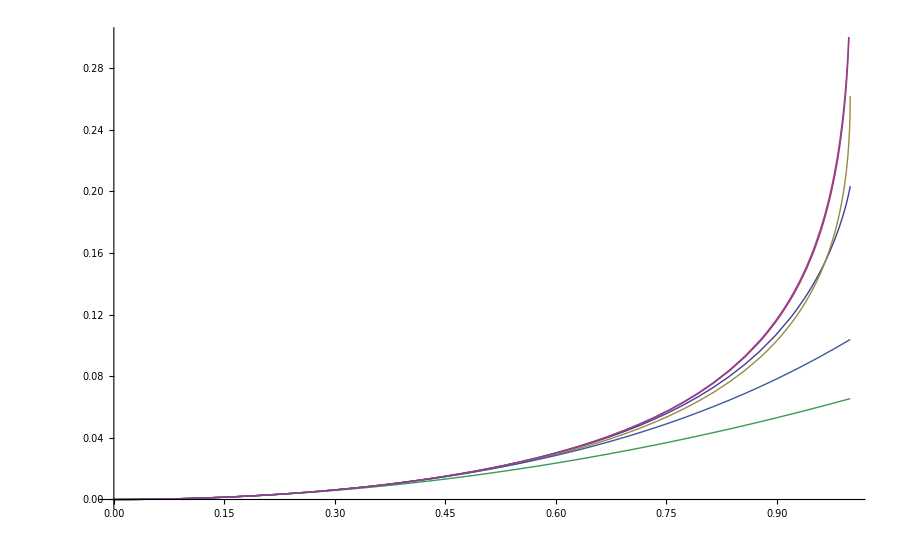

```mathematica
(* The point of this plot is that the top two curves are nearly on top of each other.  These are 
(1) our numerical best-fit solution up to 4th order and (2) Nagataki's expansion in terms of OmegaH:*)
Plot[{(pwrfullanal/.{OmH->a2OmH[a]}/.bestfit), (* best-fit numerical, 6th order *)
(pwrfullanal/.{OmH->a2OmH[a]}/.{beta->0}/.bestfit), (* best-fit numerical, 4th order *)
(pwr0anal/.{OmH->a2OmH[a]}), (* BZ2 *)
(pwr0anal/.{OmH->a/4}), (* BZ *)
(pwr0anal/.{OmH->a/4})(1+1/45(56-3 Pi^2)a^2), (* Nagataki in terms of a, 4th order *)
(pwr0anal(1+alphaNagataki(OmH)^2))/.{OmH->a2OmH[a]}}, (* Nagataki in terms of OmH, 4th order *)
{a,0,1},PlotRange->{{0,1},{0,0.3}}]
```

```mathematica
data=Table[{a2OmH[datax[[i]]],datay[[i]]-(pwr0anal/.{OmH->a2OmH[datax[[i]]]})},{i,1,Length[datax]}];
res=Fit[data,{OmH^2,OmH^4,OmH^6},OmH]
clist=CoefficientList[Collect[res-(pwrfullanal-pwr0anal),OmH],OmH]
Solve[clist==0,{alpha,beta,gamma}]
```

{}

{0,0,-0.0239455,0,1.62621-1.0472 alpha,0,-9.88772+1.0472 beta}

-0.0239455 OmH^2+1.62621 OmH^4-9.88772 OmH^6

{}

{0,0,-0.0239455,0,1.62621-1.0472 alpha,0,-9.88772+1.0472 beta}

-0.0239455 OmH^2+1.62621 OmH^4-9.88772 OmH^6

-0.0239455 OmH^2+1.62621 OmH^4-9.88772 OmH^6

{0,0,-0.0239455,0,1.62621-1.0472 alpha,0,-9.88772+1.0472 beta}

{}

```mathematica
Solve[OmH==a/(2(1+Sqrt[1-a^2])),{a}]
```

{{a→(4 OmH)/(1+4 OmH^2)}}

{{a→(4 OmH)/(1+4 OmH^2)}}

{{a→(4 OmH)/(1+4 OmH^2)}}

```mathematica
(*pwr0anal=2Pi 0.0104167 (4OmH)^2/(2Pi)^2
2Pi 0.0104167 
pwr1anal=2Pi 0.00873733 (4OmH)^2/(2Pi)^2
2Pi 0.00873733*)
```